```mathematica
ClearAll[J,L, H,g,μ, v1,v2,p1,p2,m1,m2,l1,l2,θ1,θ2,ω1,ω2,x1,x2,y1,y2,α, θ, Ω1, Ω2]
```

```mathematica
l1 = l2 = m1 = m2 = 1;
g = ϵ;
```

```mathematica
x1 = l1 Sin[θ[t]];
y1 = l1 Cos[θ[t]];
x2 = x1 + l2 Sin[α[t]+θ[t]];
y2 = y1 + l2 Cos[α[t]+θ[t]];
```

```mathematica
L = (1/2)( m1(D[x1,t]^2 +D[y1,t]^2) + m2(D[x2,t]^2 +D[y2,t]^2)) - m1 g y1 - m2 g y2//FullSimplify ;
L = FullSimplify[L/.{θ'[t]->ω1,α'[t]->ω2, θ[t]->θ, α[t]->α}];
e =FullSimplify[ D[L,ω1]ω1 + D[L,ω2]ω2 - L];
Print["L = ", L];
Print["E = ", e];
```

L = 1/2 (3 ω1^2+2 ω1 ω2+ω2^2+2 ω1 (ω1+ω2) Cos[α]-2 ϵ (2 Cos[θ]+Cos[α+θ]))

E = ω1 (ω1+ω2) Cos[α]+1/2 (3 ω1^2+2 ω1 ω2+ω2^2+4 ϵ Cos[θ]+2 ϵ Cos[α+θ])

```mathematica
Collect[L, {ω1, ω2}]
```

ω2^2/2+1/2 ω1 ω2 (2+2 Cos[α])+1/2 ω1^2 (3+2 Cos[α])-ϵ (2 Cos[θ]+Cos[α+θ])

```mathematica
M = ({{3+2Cos[α], (1+Cos[α])}, {(1+Cos[α]), 1}});
 L ==(1/2){ ω1, ω2}.M. {ω1, ω2}- g(2Cos[θ]+Cos[α+θ])//FullSimplify
```

True

```mathematica
{Ω1, Ω2} ={ω1, ω2}/.Flatten[ Solve[ p1 == D[L, ω1] && p2 == D[L, ω2], {ω1,ω2}]];
H = Collect[Expand[Simplify[{p1, p2}.{Ω1,Ω2} - L/.{ω1->Ω1,ω2->Ω2}]], {p1,p2}]//FullSimplify
Hϵ = H
```

(-p1^2+2 p1 p2-3 p2^2+2 (p1-p2) p2 Cos[α]+ϵ (-3+Cos[2 α]) (2 Cos[θ]+Cos[α+θ]))/(-3+Cos[2 α])

(-p1^2+2 p1 p2-3 p2^2+2 (p1-p2) p2 Cos[α]+ϵ (-3+Cos[2 α]) (2 Cos[θ]+Cos[α+θ]))/(-3+Cos[2 α])

```mathematica
With[ {H = H/.{p1->μ,p2->p}},
Print["H = ", Collect[H,ϵ]];
Print["μ = ", D[L, ω1]];
Print[StringRepeat["-",80]];
Print[ "θ' = " , Collect[D[H, μ]//FullSimplify,ϵ]];
Print[ "μ' = " , Collect[-D[H, θ]//FullSimplify,ϵ]];
Print[ "α' = " , Collect[D[H, p]//FullSimplify,ϵ]];
Print[ "p' = " , Collect[-D[H, α]//FullSimplify,ϵ]];
]
```

H = (-3 p^2+2 p μ-μ^2+2 p (-p+μ) Cos[α])/(-3+Cos[2 α])+ϵ (2 Cos[θ]+Cos[α+θ])

μ = 1/2 (6 ω1+2 ω2+2 ω1 Cos[α]+2 (ω1+ω2) Cos[α])

--------------------------------------------------------------------------------

θ' = (2 (p-μ+p Cos[α]))/(-3+Cos[2 α])

μ' = ϵ (2 Sin[θ]+Sin[α+θ])

α' = (2 (-3 p+μ+(-2 p+μ) Cos[α]))/(-3+Cos[2 α])

p' = (4 (p-μ+p Cos[α]) (2 p+(p-μ) Cos[α]) Sin[α])/(-3+Cos[2 α])^2+ϵ (Cos[θ] Sin[α]+Cos[α] Sin[θ])

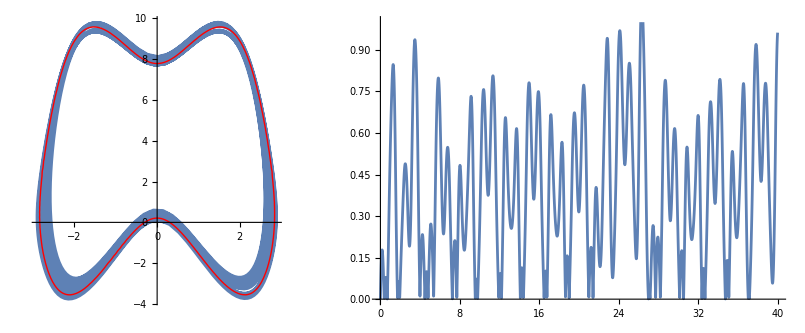

```mathematica
rules = {θ->θ[t], μ->μ[t], α->α[t], p->p[t]};
With[{T = 40,ϵ0=1},
H=(Hϵ/.{p1->μ,p2->p})/.{ϵ->ϵ0};
sol =
NDSolve[
{
 θ'[t] == (D[H,μ]/.rules),
θ[0] == 3Pi/4,
μ'[t] == (-D[H,θ]/.rules),
μ[0] == 10,
α'[t] == (D[H,p]/.rules),
α[0] == Pi/16,
p'[t] == (-D[H,α]/.rules),
p[0] == 0
},
{θ,μ,α,p},
{t, 0, T}
];
h0 = ((H/.rules)/.sol)/.{t->0}//First;
μ0 = (μ[t]/.sol)/.{t->0}//First;
H0=(Hϵ/.{p1->μ,p2->p})/.{ϵ->0};
H0 = H0/.{θ->3Pi/4, μ->10};
GraphicsRow[
{
Show[
ParametricPlot[Evaluate[{α[t],p[t]}/.sol],{t,0,T}, AspectRatio->1],
ContourPlot[H0, {α,-Pi,Pi}, {p, -4,10}, Contours->{h0},ContourShading->None, ContourStyle->Red]
],
Plot[Evaluate[Abs[μ[t]-μ0]/.sol],{t,0,T},PlotRange->{0,ϵ0}]
},
ImageSize->Automatic
]
]
```

```mathematica
With[ {H = H/.{p1->μ,p2->p}},
Print["H = ", Collect[H,ϵ]];
Print["μ = ", D[L, ω1]];
Print[StringRepeat["-",80]];
Print[ "θ' = " , Collect[D[H, μ]//FullSimplify,ϵ]];
Print[ "μ' = " , Collect[-D[H, θ]//FullSimplify,ϵ]];
Print[ "α' = " , Collect[D[H, p]//FullSimplify,ϵ]];
Print[ "p' = " , Collect[-D[H, α]//FullSimplify,ϵ]];
]
```

H = (-3 p^2+2 p μ-μ^2+2 p (-p+μ) Cos[α])/(-3+Cos[2 α])+ϵ (2 Cos[θ]+Cos[α+θ])

μ = 1/2 (6 ω1+2 ω2+2 ω1 Cos[α]+2 (ω1+ω2) Cos[α])

--------------------------------------------------------------------------------

θ' = (2 (p-μ+p Cos[α]))/(-3+Cos[2 α])

μ' = ϵ (2 Sin[θ]+Sin[α+θ])

α' = (2 (-3 p+μ+(-2 p+μ) Cos[α]))/(-3+Cos[2 α])

p' = (4 (p-μ+p Cos[α]) (2 p+(p-μ) Cos[α]) Sin[α])/(-3+Cos[2 α])^2+ϵ (Cos[θ] Sin[α]+Cos[α] Sin[θ])

```mathematica
S = (μ0 + Sqrt[ϵ] η)θ;
ϕ == D[S,η ]
μ == D[S, θ]
```

ϕ==√ϵ θ

μ==√ϵ η+μ0

```mathematica
Hexpan = H/.{p1->(μ0 + Sqrt[ϵ] η), p2->p, θ->ϕ/Sqrt[ϵ]} ;
With[ {H = Hexpan},
Print["H = ", Collect[H,ϵ]];
Print[StringRepeat["-",80]];
Print[ "ϕ' = " , Collect[Simplify[D[H, η]/.{ϵ->δ^2},δ>0],δ]];
Print[ "η' = " ,Collect[Simplify[-D[H, ϕ]/.{ϵ->δ^2},δ>0],δ]];
Print[ "α' = " , Collect[Simplify[D[H, p]/.{ϵ->δ^2},δ>0],δ]];
Print[ "p' = " ,Collect[Simplify[-D[H, α]/.{ϵ->δ^2},δ>0],δ]];
]
```

H = (√ϵ (2 p η-2 η μ0+2 p η Cos[α]))/(-3+Cos[2 α])+(-3 p^2+2 p μ0-μ0^2-2 p^2 Cos[α]+2 p μ0 Cos[α])/(-3+Cos[2 α])+(ϵ (-η^2+(-3+Cos[2 α]) (2 Cos[ϕ/(√ϵ)]+Cos[α+ϕ/(√ϵ)])))/(-3+Cos[2 α])

--------------------------------------------------------------------------------

ϕ' = -(2 δ^2 η)/(-3+Cos[2 α])+(2 δ (p-μ0+p Cos[α]))/(-3+Cos[2 α])

η' = δ (2 Sin[ϕ/δ]+Sin[α+ϕ/δ])

α' = (2 δ (η+η Cos[α]))/(-3+Cos[2 α])+(2 (-3 p+μ0-2 p Cos[α]+μ0 Cos[α]))/(-3+Cos[2 α])

p' = (δ (-8 η (p-μ0) Cos[α] Sin[α]-2 p η (5+Cos[2 α]) Sin[α]))/(-3+Cos[2 α])^2+(2 p^2 (5+Cos[2 α]) Sin[α]-2 p μ0 (5+Cos[2 α]) Sin[α]+6 p^2 Sin[2 α]-4 p μ0 Sin[2 α]+2 μ0^2 Sin[2 α])/(-3+Cos[2 α])^2+(δ^2 (2 η^2 Sin[2 α]+(-3+Cos[2 α])^2 Sin[α+ϕ/δ]))/(-3+Cos[2 α])^2

```mathematica
With[ {H = H/.{p1->(μ0 + ϵ η), p2->p, θ -> ϕ/ϵ}},
Print["H = ", Collect[H,ϵ]];
Print[StringRepeat["-",80]];
Print[ "ϕ' = " , Collect[D[H, η]//FullSimplify,ϵ]];
Print[ "η' = " , Collect[-D[H, ϕ]//FullSimplify,ϵ]];
Print[ "α' = " , Collect[D[H, p]//FullSimplify,ϵ]];
Print[ "p' = " , Collect[-D[H, α],ϵ]];
]
```

H = -(ϵ^2 η^2)/(-3+Cos[2 α])+(-3 p^2+2 p μ0-μ0^2-2 p^2 Cos[α]+2 p μ0 Cos[α])/(-3+Cos[2 α])+(ϵ (2 p η-2 η μ0+2 p η Cos[α]+(-3+Cos[2 α]) (2 Cos[ϕ/ϵ]+Cos[α+ϕ/ϵ])))/(-3+Cos[2 α])

--------------------------------------------------------------------------------

ϕ' = -(2 ϵ^2 η)/(-3+Cos[2 α])+(2 ϵ (p-μ0+p Cos[α]))/(-3+Cos[2 α])

η' = 2 Sin[ϕ/ϵ]+Sin[α+ϕ/ϵ]

α' = (2 ϵ (η+η Cos[α]))/(-3+Cos[2 α])+(2 (-3 p+μ0-2 p Cos[α]+μ0 Cos[α]))/(-3+Cos[2 α])

p' = -(2 p^2 Sin[α])/(-3+Cos[2 α])+(2 p μ0 Sin[α])/(-3+Cos[2 α])+(6 p^2 Sin[2 α])/(-3+Cos[2 α])^2+(2 ϵ^2 η^2 Sin[2 α])/(-3+Cos[2 α])^2-(4 p μ0 Sin[2 α])/(-3+Cos[2 α])^2+(2 μ0^2 Sin[2 α])/(-3+Cos[2 α])^2+(4 p^2 Cos[α] Sin[2 α])/(-3+Cos[2 α])^2-(4 p μ0 Cos[α] Sin[2 α])/(-3+Cos[2 α])^2+ϵ ((2 p η Sin[α])/(-3+Cos[2 α])-(4 p η Sin[2 α])/(-3+Cos[2 α])^2+(4 η μ0 Sin[2 α])/(-3+Cos[2 α])^2-(4 p η Cos[α] Sin[2 α])/(-3+Cos[2 α])^2+Sin[α+ϕ/ϵ])

```mathematica
rule = {μ->(μ0 + ϵ η)};
With[ {H = H/.{p1->μ, p2->p}},
Print["H = ", Collect[H,ϵ]/.rule];
Print[StringRepeat["-",80]];
Print[ "θ' = " , Collect[D[H, μ]/.rule,ϵ]];
Print[ "η' = " , Collect[-D[H, θ]/ϵ/.rule,ϵ]];
Print[ "α' = " , Collect[D[H, p]/.rule,ϵ]];
Print[ "p' = " , Collect[-D[H, α]/.rule,ϵ]];
]
Print[StringRepeat["-",80]];
With[ {H = H/.{p1->μ, p2->p}},
Print["H = ", Collect[H,ϵ]/.rule];
Print[StringRepeat["-",80]];
Print[ "θ' = " , FullSimplify[D[H, μ]/.rule]];
Print[ "η' = " , FullSimplify[-D[H, θ]/ϵ/.rule]];
Print[ "α' = " , FullSimplify[D[H, p]/.rule]];
Print[ "p' = " , FullSimplify[-D[H, α]/.rule]];
]
```

H = (-3 p^2+2 p μ-μ^2+2 p (-p+μ) Cos[α])/(-3+Cos[2 α])+ϵ (2 Cos[θ]+Cos[α+θ])

--------------------------------------------------------------------------------

θ' = (2 (p-μ+p Cos[α]))/(-3+Cos[2 α])

μ' = ϵ (2 Sin[θ]+Sin[α+θ])

α' = (2 (-3 p+μ+(-2 p+μ) Cos[α]))/(-3+Cos[2 α])

p' = (4 (p-μ+p Cos[α]) (2 p+(p-μ) Cos[α]) Sin[α])/(-3+Cos[2 α])^2+ϵ (Cos[θ] Sin[α]+Cos[α] Sin[θ])

--------------------------------------------------------------------------------

H = (-3 p^2+2 p (ϵ η+μ0)-(ϵ η+μ0)^2+2 p (-p+ϵ η+μ0) Cos[α])/(-3+Cos[2 α])+ϵ (2 Cos[θ]+Cos[α+θ])

--------------------------------------------------------------------------------

θ' = -(2 ϵ η)/(-3+Cos[2 α])+(2 p-2 μ0+2 p Cos[α])/(-3+Cos[2 α])

η' = 2 Sin[θ]+Sin[α+θ]

α' = (ϵ (2 η+2 η Cos[α]))/(-3+Cos[2 α])+(-6 p+2 μ0-4 p Cos[α]+2 μ0 Cos[α])/(-3+Cos[2 α])

p' = -(2 p^2 Sin[α])/(-3+Cos[2 α])+(2 p μ0 Sin[α])/(-3+Cos[2 α])+(6 p^2 Sin[2 α])/(-3+Cos[2 α])^2+(2 ϵ^2 η^2 Sin[2 α])/(-3+Cos[2 α])^2-(4 p μ0 Sin[2 α])/(-3+Cos[2 α])^2+(2 μ0^2 Sin[2 α])/(-3+Cos[2 α])^2+(4 p^2 Cos[α] Sin[2 α])/(-3+Cos[2 α])^2-(4 p μ0 Cos[α] Sin[2 α])/(-3+Cos[2 α])^2+ϵ ((2 p η Sin[α])/(-3+Cos[2 α])-(4 p η Sin[2 α])/(-3+Cos[2 α])^2+(4 η μ0 Sin[2 α])/(-3+Cos[2 α])^2-(4 p η Cos[α] Sin[2 α])/(-3+Cos[2 α])^2+Sin[α+θ])

--------------------------------------------------------------------------------

H = (-3 p^2+2 p (ϵ η+μ0)-(ϵ η+μ0)^2+2 p (-p+ϵ η+μ0) Cos[α])/(-3+Cos[2 α])+ϵ (2 Cos[θ]+Cos[α+θ])

--------------------------------------------------------------------------------

θ' = (2 (p-ϵ η-μ0+p Cos[α]))/(-3+Cos[2 α])

η' = 2 Sin[θ]+Sin[α+θ]

α' = (2 (-3 p+ϵ η+μ0+(-2 p+ϵ η+μ0) Cos[α]))/(-3+Cos[2 α])

p' = (2 p (-p+ϵ η+μ0) Sin[α])/(-3+Cos[2 α])+(2 (3 p^2-2 p (ϵ η+μ0)+(ϵ η+μ0)^2+2 p (p-ϵ η-μ0) Cos[α]) Sin[2 α])/(-3+Cos[2 α])^2+ϵ Sin[α+θ]

```mathematica
Print["z = ", {θ, η,α, p}//MatrixForm];
Print["z' = ", "f_0(z) + " <> "ϵ f_1(z) + " <> "ϵ^2 f_2(z)"];
Print["f_0 = ", {(2 (p-μ0+p Cos[α]))/(-3+Cos[2 α]),2 Sin[θ]+Sin[α+θ],(2 (-3 p+μ0+(-2 p+μ0) Cos[α]))/(-3+Cos[2 α]),-(2 p^2 Sin[α])/(-3+Cos[2 α])+(2 p μ0 Sin[α])/(-3+Cos[2 α])+(6 p^2 Sin[2 α])/(-3+Cos[2 α])^2-(4 p μ0 Sin[2 α])/(-3+Cos[2 α])^2+(2 μ0^2 Sin[2 α])/(-3+Cos[2 α])^2+(4 p^2 Cos[α] Sin[2 α])/(-3+Cos[2 α])^2-(4 p μ0 Cos[α] Sin[2 α])/(-3+Cos[2 α])^2}//FullSimplify//MatrixForm];
Print["f_1 = ", {-(2 η)/(-3+Cos[2 α]) ,0,(2 η+2 η Cos[α])/(-3+Cos[2 α]),(2 p η Sin[α])/(-3+Cos[2 α])-(4 p η Sin[2 α])/(-3+Cos[2 α])^2+(4 η μ0 Sin[2 α])/(-3+Cos[2 α])^2-(4 p η Cos[α] Sin[2 α])/(-3+Cos[2 α])^2+Sin[α+θ]}//FullSimplify//MatrixForm];
Print["f_2 = ", {0, 0, 0, (2 η^2 Sin[2 α])/(-3+Cos[2 α])^2}//MatrixForm]
```

z = (θ
η
α
p)

z' = f_0(z) + ϵ f_1(z) + ϵ^2 f_2(z)

f_0 = ((2 (p-μ0+p Cos[α]))/(-3+Cos[2 α])
2 Sin[θ]+Sin[α+θ]
(2 (-3 p+μ0+(-2 p+μ0) Cos[α]))/(-3+Cos[2 α])
(2 (2 (3 p^2-2 p μ0+μ0^2) Cos[α]+p (p-μ0) (5+Cos[2 α])) Sin[α])/(-3+Cos[2 α])^2)

f_1 = (-(2 η)/(-3+Cos[2 α])
0
(2 η (1+Cos[α]))/(-3+Cos[2 α])
-(2 η (4 (p-μ0) Cos[α]+p (5+Cos[2 α])) Sin[α])/(-3+Cos[2 α])^2+Sin[α+θ])

f_2 = (0
0
0
(2 η^2 Sin[2 α])/(-3+Cos[2 α])^2)